```mathematica
(*==================Aquí inician los calculos de Press-Schechter=====================================*)
(*Do[camb[i]=Import[If[i==1,$HomeDirectory<>"/Google \Drive/Cosmomc_Planck_Dic13/camb/test_matterpower.dat",$HomeDirectory<>"/Google\Drive/Cosmomc_Planck_Dic13/camb/test_matterpower_"<>ToString[i]<>".dat"],"Data"],{i,1,100}];*)
Do[cambqnv[j,l,i]=Import[If[i==1,$HomeDirectory<>"/MEGA/Cosmomc_Planck_Dic13/cosmomc_v1_5Mayo/camb/"<>"test_"<>ToString[j]<>ToString[l]<>"_matterpower.dat",$HomeDirectory<>"/MEGA/Cosmomc_Planck_Dic13/cosmomc_v1_5Mayo/camb/"<>"test_"<>ToString[j]<>ToString[l]<>"_matterpower_"<>ToString[i]<>".dat"],"Data"],{i,1,201},{j,{-8,-6,-4,-2,0,20}},{l,{0,4,10}}];(*Do[evolveqv[k]=Import[$HomeDirectory<>"/Cosmomc_Planck_Dic13/cosmomc_v1_5Mayo/camb/"<>"evolve_"<>ToString[k]<>ToString[j]<>ToString[l]<>".dat","Data"],{k,{0.0001,0.001,0.01,0.1,1,10}},{j,{-8,-6,-4,-2,0,20}},{l,{0,1,2,4,6,10}}];*)
```

```mathematica
(*Needs to work*)
Needs["NumericalDifferentialEquationAnalysis`"]
(*Función Subscript[Ω, R](a(t))∼1/a^4*)
FOrad[y_,omer_]:=omer/y^4;
(*Función Subscript[Ω, b](a(t))∼1/a^3*)
FObar[y_,omeb_]:=omeb/y^3;

(*Función Subscript[Ω, Λ](a)*)
FOde[y_,omede_]:=omede;
(*Razón de expanción 3000 Mpc Subscript[H, o]*)
h=0.704;
(*Esta es la omega de materia, que incluye materia oscura y  materia bariónica Subscript[Ω, M]^o h^2*)
ome=0.1598;
(*Índice espectral*)
n=0.968;
(*Subscript[Ω, b]^o h^2*)
omebar=0.02255;
(*Esta es la omega de materia oscura*)
omedm=ome-omebar;
(*Subscript[Ω, γ]^o h^2*)
omefot=2.47*10^-5;
Tcmb=2.75/11605;
(*Subscript[Ω, ν]^o h^2*)
omeneu=(21/8)(4/11)^(4/3)(2.47*10^-5);


(*Omega total de radiación a hoy*)
omerad=omeneu+omefot;

(*Esta es la condición de planitud, desde la cual imponemos que  Subscript[Ω, M]^o+Subscript[Ω, Λ]^o≈1*)
omeconst=h*h-ome-omerad;
hfunc[y_]:=(1/3000)Sqrt[(FOrad[y,omerad]+FObar[y,omebar]+omedm(1/y)^3+FOde[y,omeconst])];

(*Δ^2(q)*)
Ncua=2.45*10^-9;

FOdm[y_,omed_,ac_,qn_]:=If[y<ac,(omed*ac/y^4)Exp[-qn^2/2(ac^2-1)],(omed/y^3)Exp[-qn^2/2(ac^2-ac^2/y^2)]] ;


FOdm2[y_,omed_,ac_,qn_]:=If[y<ac,(omed*ac/y^4),(omed/y^3)] ;


(*Función w(a(t)), obtenida a partir de P(t)/ρ(t)=w(t) y ρ'=-3H(ρ+P)*)
Fw[y_,omedm_,ac_,qn_]:= If[y<ac,1/3,qn/3 (ac/y)^2](*-y D[FOdm[y,omedm,ades],y]/(3FOdm[y,omedm,ades])-1*);
dFw[y_,omedm_,ac_,qn_]:= If[y<ac,0,-2*qn/3 (ac/y)^2/y];

DFw[y_,omedm_,ac_,qn_]:=Fw[y,omedm,ac,qn]-1/3 y dFw[y,omedm,ac,qn]/(1+Fw[y,omedm,ac,qn]);
hfun[y_?NumberQ,ac_?NumberQ,qn_?NumberQ,ome_?NumberQ]:=(1/3000)((FOrad[y,omerad]+FObar[y,omebar]+FOdm[y,ome,ac,qn]+FOde[y,omeconst]))^(1/2);
(*Velocidad de la particula *)
vc[y_?NumberQ,ac_?NumberQ,qn_?NumberQ]:=If[y<ac,1,qn(ac/y)];

(*Densidad Critica del universo dada en 10^8 M_⊙/Mpc^3*)
densidad= 1.2*10^3;
(*Masa contenidad en una esfera de radio Subscript[λ, FS]/2 dada en 10^8 M_⊙ *)
masa[a_?NumberQ,ac_?NumberQ,qn_?NumberQ]:=(4 Pi/3) densidad(lambda[a,ac,qn]/2)^3;
(*Subscript[λ, FS] para la cual ua esfera de radio Subscript[λ, FS]/2 contiene la masa m media en unidades de  10^8 M_⊙ *)
lambdaM[m_?NumberQ]:=2(3m/(4 Pi densidad))^(1/3);
(*Masa Subscript[m, c] de la particula dada por la relacion Subscript[m, c]=3Subscript[T, c]/Subscript[v, c]^2 dada en keV*)
mc[ac_?NumberQ,qn_?NumberQ]:=3((omedm/ac^3)Exp[-qn^2/2(ac^2-1)]/omefot)^(1/4) Tcmb/qn^2/1000;
(*Masa Subscript[m, w] de la particula dada por la relacion Subscript[m, w]=3 Subscript[T, c] dada en keV*)
mW[ac_?NumberQ]:=3((omedm/ac^3)Exp[-1/2(ac^2-1)]/omefot)^(1/4) Tcmb/1000;
(*Subscript[a, c] para el cual se la particula tiene una masa Subscript[m, c] y un cambio en la velocidad en la transicion de cero.*)
acmc0[m_?NumberQ]:=ac/.FindRoot[mc[ac,1]==m,{ac,10^-12}];
(*Subscript[a, c] para el cual la particula tiene una Subscript[λ, FS] y un cambio en la velocidad en la transicion de cero.*)
(*====================================================================================*)

(*Calculo de Subscript[λ, FS](Subscript[a, c],Subscript[v, c])*)
f[y_?NumberQ,omed_?NumberQ,ac_?NumberQ,a_?NumberQ]:=NIntegrate[1/(x^2 hfun[x,ac,a,omed]),{x,0,ac},Method->{"GaussKronrodRule","Points"->10},MaxRecursion->1000]+NIntegrate[(a ac/x)/(x^2 hfun[x,ac,a,omed]),{x,ac,y},Method->{"GaussKronrodRule","Points"->10},MaxRecursion->1000];
acLambda0[λ_?NumberQ]:=ac/.FindRoot[f[1,omedm,ac,1]==λ,{ac,10^-12}]
(*Longitud de FreeStreaming Subscript[λ, FS] dada por la integral ∫vⅆτ en unidades de Mpc*)
lambda[y_?NumberQ,omed_?NumberQ,ac_?NumberQ,a_?NumberQ]:=NIntegrate[1/(x^2 hfun[x,ac,a,omed]),{x,0,ac},Method->{"GaussKronrodRule","Points"->10},MaxRecursion->1000]+NIntegrate[(a ac/x)/(x^2 hfun[x,ac,a,omed]),{x,ac,y},Method->{"GaussKronrodRule","Points"->10},MaxRecursion->1000];

masa1=10;
qc[ac_?NumberQ,qn_?NumberQ]:=omedm(10^-25/27)densidad(FOdm[ac,omedm,ac,qn])/qn^3;Q1=10^-6;Q2=10^-4;masa2=10^-1;
Hyperlink["Link Articulo m_c", "http://arxiv.org/abs/1311.5223"];
(*Valor aceptado en el arituclo de http://arxiv.org/abs/1311.5223  donde encuentran los valores de Subscript[m, c]> 3.3 KeV y Subscript[λ, FS]< 2 10^8 M_⊙*)

mc1=3.3;mc2=10^9;
(*===================== Funcion rho_c(a,Subscript[a, c],Subscript[v, c])=================================*)
rhoc[x_?NumberQ,ac_?NumberQ,y_?NumberQ]:=If[x<ac,ac Exp[-(y ac)^2/(2 ac^2)(1-ac^2)]/x^4, Exp[-(y ac)^2/(2 x^2)(1-x^2)]/x^3] ;
(*===================== Funcion que calcula el valor de Subscript[e, eq] dado por la solucion de Subscript[ρ, R](a)=Subscript[ρ, B](a)+Subscript[ρ, DM](a)*)aeq[ac_?NumberQ,vc_?NumberQ,aeQ_?NumberQ,ratDm_?NumberQ]:= Module[{x,ac0=ac,y0=vc},x/.FindRoot[aeQ==( (1-ratDm) x +x^4 ratDm If[x<ac,ac/x^4, Exp[-(vc ac)^2/(2 x^2)(1-x^2)]/x^3]),{x,10^-10}][[1]]];

(*===================== Funcion de  Subscript[ρ, R](a)-Subscript[ρ, B](a)-Subscript[ρ, DM](a)=====================================================*)aeqdiff[x_?NumberQ,ac_?NumberQ,y_?NumberQ,aeQ_?NumberQ,ratDm_?NumberQ]:= aeQ-( (1-ratDm) x +x^4 ratDm If[x<ac,ac/x^4, Exp[-(y ac)^2/(2 x^2)(1-x^2)]/x^3])
(*===================== Calculo del valor de Subscript[a, c] para el cual tenemos Subscript[a, eq]<0===================================*)
logacneg[vc_?NumberQ,aeq0_?NumberQ,ratDm_?NumberQ]:=
Module[{a1,a2,a3,ae1,error,test},
error=N[10^-2];
a1=-10;
a2=0;
While[error>10^-10,
test=aeq[N[10^a1],N[vc],N[aeq0],N[ratDm]]*aeq[N[10^a2],N[vc],N[aeq0],N[ratDm]];
If[test>0,a3=Null;Break[],Null];
a3=N[(a1+a2)/2];
ae1=aeq[N[10^a3],N[vc],N[aeq0],N[ratDm]];
If[ae1>=0,a1=a3,a2=a3];
error=Abs[ae1]];
N[a3]
]

(*==============================Util para la otra Función======================================*)
logacnegmod[vc_?NumberQ,aeq0_?NumberQ,ratDm_?NumberQ]:=
Module[{a1,a2,a3,ae1,error,test},
error=N[10^-2];
a1=-10;
a2=5;
While[error>10^-10,
test=aeq[N[10^a1],N[vc],N[aeq0],N[ratDm]]*aeq[N[10^a2],N[vc],N[aeq0],N[ratDm]];
If[test>0,a3=Null;Break[],Null];
a3=N[(a1+a2)/2,10];
ae1=aeq[N[10^a3],N[vc],N[aeq0],N[ratDm]];
If[ae1>=0,a1=a3,a2=a3];
error=Abs[ae1]];
N[a3]
]
(*===================== Calculo del valor de Subscript[a, c]  para el cual tenemos Subscript[a, eqneg]=1*)
logaeq[vc_?NumberQ,ratDm_?NumberQ]:=
Module[{a1,a2,a3,ae1,error,test},
error=N[10^-2];
a1=-10;
a2=2;
While[error>10^-8,
test=logacnegmod[N[vc],N[10^a1],N[ratDm]]*logacnegmod[N[vc],N[10^a2],N[ratDm]];
If[test>0,a3=0;Break[],Null];
a3=N[(a1+a2)/2,10];
ae1=1-logacnegmod[N[10^a3],N[vc],N[10^a3],N[ratDm]];
If[ae1>=0,a1=a3,a2=a3];
error=Abs[ae1]];
N[a3]
];
(*===================== ac para la cual tenemos una Subscript[m, w](Subscript[a, c])=Subscript[m, w]*)
transacvc[mwc_?NumberQ]:=acc/.FindRoot[{mW[acc]==mwc},{acc,10^-15},MaxIterations->Infinity][[1]];
(*Metodo para integrar numericamente utilizando el metodo de cuadratura de Gauss-Legendre*)

Clear[w];nd = 150;w=GaussianQuadratureWeights[nd,-1,1];
integral [f_,a_,b_]:=((b-a)/2)Sum[f[#]&[ (b-a)/2 w[[j,1]]+(b+a)/2]w[[j,2]],{j,1,nd}];

Fwind[y_]:=3(Sin[y]/y^3-Cos[y]/y^2);

numk[l_,j_,z_] := Dimensions[cambqnv[l,j,z]][[1]];
kmin[l_,j_,z_]:= cambqnv[l,j,z][[1,1]];
kmax[l_,j_,z_] := cambqnv[l,j,z][[numk[l,j,z],1]];nk[logk_,l_,j_,z_]:=IntegerPart[ (logk-Log[10,kmin[l,j,z]])/Log[10,kmax[l,j,z]/kmin[l,j,z]]*(numk[l,j,z]-1)]+1;
P[logk_,l_,j_,z_]:=cambqnv[l,j,z][[nk[logk,l,j,z],2]];

Δ[R_,logk_,l_,j_,z_]:=(1/2 Pi^2)(Fwind[Exp[logk]R])^2 Exp[3 logk]P[logk,l,j,z];

σ[R_,l_,j_,z_]:=0.81/21.18457487637353*Sqrt[ integral[(Δ[R,#,l,j,z]&),Log[10,kmin[l,j,z]],Log[10,kmax[l,j,z]]]]; 
Tableσ[R_,l_?NumberQ,j_?NumberQ,znum_?NumberQ]:=
																Table[{3(201-z)/200,σ[R,l,j,z]},{z,201,znum,-1}];Subscript[σ, 8]=σ[8,20,10,201];
Growth[z_,l_,j_]:=
201*(σ[8,l,j,IntegerPart[(603-200z)/3]-1]/Subscript[σ, 8]-σ[8,l,j,IntegerPart[(603-200z)/3]]/Subscript[σ, 8])/3(z-(603-3IntegerPart[(603-200z)/3])/200)+σ[8,l,j,IntegerPart[(603-200z)/3]]/Subscript[σ, 8];σ8[z_,l_,j_]:=201*(σ[8,l,j,IntegerPart[(603-200z)/3]-1]-σ[8,l,j,IntegerPart[(603-200z)/3]])/3(z-(603-3IntegerPart[(603-200z)/3])/200)+σ[8,l,j,IntegerPart[(603-200z)/3]];
fsigma8[z_,l_,j_]:=201*(σ[8,l,j,IntegerPart[(603-200z)/3]-1]-σ[8,l,j,IntegerPart[(603-200z)/3]])/3(z-(603-3IntegerPart[(603-200z)/3])/200)+σ[8,l,j,IntegerPart[(603-200z)/3]]201*(σ[8,l,j,IntegerPart[(603-200z)/3]-1]/Subscript[σ, 8]-σ[8,l,j,IntegerPart[(603-200z)/3]]/Subscript[σ, 8])/3(z-(603-3IntegerPart[(603-200z)/3])/200)+σ[8,l,j,IntegerPart[(603-200z)/3]]/Subscript[σ, 8];
Fmasses[R_,l_?NumberQ,j_?NumberQ,z_?NumberQ]:=2.84 ((FObar[1/(1+3(201-z)/200),omebar]+FOdm[1/(1+3(201-z)/200),omedm,Exp[-l]*10^-5,Exp[-j]])/(1+3(201-z)/200)^3)( R)^3/h^2;
TableFmasses[R_,l_?NumberQ,j_?NumberQ,znum_?NumberQ]:=
																Table[{3(201-z)/200,Fmasses[R,l,j,z]},{z,201,znum,-1}];
Dσ[R_?NumberQ,l_?NumberQ,j_?NumberQ,z_?NumberQ]:=D[σ[x,l,j,z],x]/.x->R;
TableDσ[R_,l_?NumberQ,j_?NumberQ,znum_?NumberQ]:=
																Table[{3(201-z)/200,Dσ[R,l,j,z]},{z,201,znum,-1}];
Fr[M_,l_,j_,z_]:=10(M h^2(1+3(201-z)/2003(201-z)/200)^3/(2.84(omebar(1+3(201-z)/200)^3+FOdm[1/(1+3(201-z)/200),omedm,Exp[-l]*10^-5,Exp[-j]])))^(1/3);
TableFr[R_,l_?NumberQ,j_?NumberQ,znum_?NumberQ]:=
																Table[{3(201-z)/200,Fr[R,l,j,z]},{z,201,znum,-1}];

dn[R_,deltac_?NumberQ,l_?NumberQ,j_?NumberQ,z_?NumberQ]:=(2.84)√(2/Pi)(1/(3 Fmasses[R,l,j,z]^2 σ[R,l,j,z]))deltac   (omebar/h^2(1+3(201-z)/200)^3+FOdm[1/(1+3(201-z)/200),omedm,Exp[-l]*10^-5,Exp[-j]]/h^2)/(1+3(201-z)/200)^3 Exp[-deltac^2/(2 σ[R,l,j,z]^2)](-(R/σ[R,l,j,z])Dσ[R,l,j,z]);
Tabledn[R_,deltac_?NumberQ,l_?NumberQ,j_?NumberQ,znum_?NumberQ]:=Table[{3(201-z)/200,dn[R,deltac,l,j,z]},{z,201,znum,-1}];

nM[M_?NumberQ(*10^8 masas solares*),deltac_?NumberQ,l_?NumberQ,j_?NumberQ,z_?NumberQ]:=integral[dn[#,deltac,l,j,z]&,Log[10,Fr[M,l,j,z]],10000];
TablenM[M_?NumberQ(*10^8 masas solares*),deltac_?NumberQ,l_?NumberQ,j_?NumberQ,znum_?NumberQ]:=Table[{3(201-z)/200,nM[M,deltac,l,j,z]},{z,201,znum,-1}];


rcom[l_?NumberQ,j_?NumberQ,z_?NumberQ]:= integral[(1/hfun[1/(1+#),Exp[-l]*10^-5,Exp[-j],omedm])&,0,3(201-z)/200];

Tablercom[l_?NumberQ,j_?NumberQ,znum_?NumberQ]:=Table[{3(201-z)/200,rcom[l,j,z]},{z,201,znum,-1}];
dVdzdΩ[l_?NumberQ,j_?NumberQ,z_?NumberQ]:=(Pi/180)^2 rcom[l,j,z]^2/hfun[1/(1+3(201-z)/200),Exp[-l]*10^-5,Exp[-j],omedm];
TabledVdzdΩ[l_?NumberQ,j_?NumberQ,znum_?NumberQ]:=Table[{3(201-z)/200,dVdzdΩ[l,j,z]},{z,201,znum,-1}];
Tabledhfun[l_?NumberQ,j_?NumberQ,znum_?NumberQ]:=Table[{3(201-z)/200,hfun[1/(1+3(201-z)/200),Exp[-l]*10^-5,Exp[-j],omedm]},{z,201,znum,-1}];

dNdz[M_?NumberQ,deltac_?NumberQ,l_?NumberQ,j_?NumberQ,znum_?NumberQ]:=Table[{3(201-z)/200,dVdzdΩ[l,j,z]nM[M,deltac,l,j,z]},{z,201,znum,-1}];
```

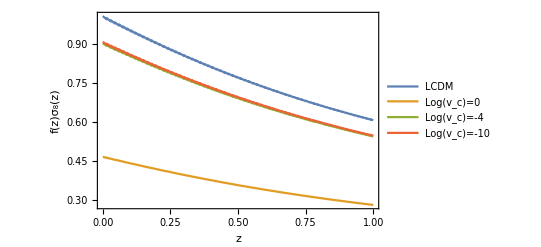

```mathematica
Plot[{fsigma8[z,20,10],fsigma8[z,-8,0],fsigma8[z,-8,4],fsigma8[z,-8,10]},{z,0,1},Frame->True,FrameLabel->{"z","f(z)σ_8(z)",None,None},PlotLegends->{"LCDM","Log(v_c)=0","Log(v_c)=-4","Log(v_c)=-10"}]
```

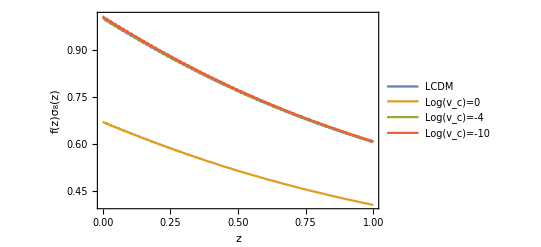

```mathematica
Plot[{fsigma8[z,20,10],fsigma8[z,-6,0],fsigma8[z,-6,4],fsigma8[z,-6,10]},{z,0,1},Frame->True,FrameLabel->{"z","f(z)σ_8(z)",None,None},PlotLegends->{"LCDM","Log(v_c)=0","Log(v_c)=-4","Log(v_c)=-10"}]
```

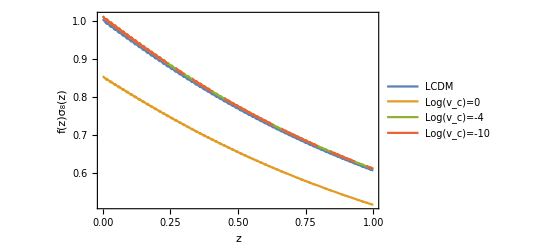

```mathematica
Plot[{fsigma8[z,20,10],fsigma8[z,-4,0],fsigma8[z,-4,4],fsigma8[z,-4,10]},{z,0,1},Frame->True,FrameLabel->{"z","f(z)σ_8(z)",None,None},PlotLegends->{"LCDM","Log(v_c)=0","Log(v_c)=-4","Log(v_c)=-10"}]
```

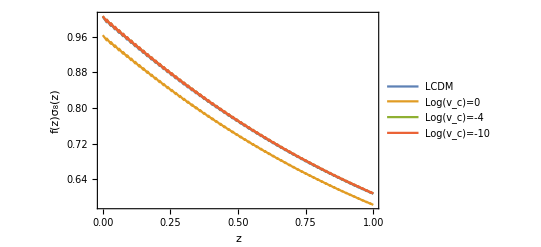

```mathematica
Plot[{fsigma8[z,20,10],fsigma8[z,-2,0],fsigma8[z,-2,4],fsigma8[z,-2,10]},{z,0,1},Frame->True,FrameLabel->{"z","f(z)σ_8(z)",None,None},PlotLegends->{"LCDM","Log(v_c)=0","Log(v_c)=-4","Log(v_c)=-10"}]
```

```mathematica
Save["DefinicionesMathematica",{σ,σc}]
```

```mathematica
Get["DefinicionesMathematica"];
```

```mathematica
σ[10,0,0,201]
```

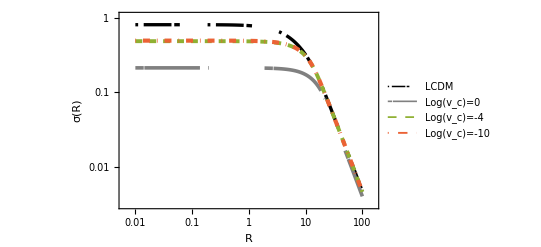

```mathematica
LogLogPlot[{σ[R,20,10,100],σ[R,-8,0,100],σ[R,-8,4,100],σ[R,-8,10,100]},{R,0.01,100},Frame->True,PlotStyle->{
{Black,Dashing[{0.005,0.01,0.05}],Thickness[0.006]},
{Gray,Dashing[{0.015,0.001,0.1}],Thickness[0.0065]},
{Dashed,Thickness[0.007]},
{DotDashed,Thickness[0.0075]}},PlotRange->All,FrameLabel->{"R","σ(R)",None,None},FrameStyle->Directive[{17}],PlotLegends->{"LCDM","Log(v_c)=0","Log(v_c)=-4","Log(v_c)=-10"}]
```

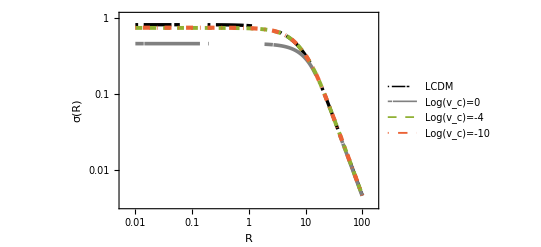

```mathematica
LogLogPlot[{σ[R,20,10,100],σ[R,-4,0,100],σ[R,-4,4,100],σ[R,-4,10,100]},{R,0.01,10^2},Frame->True,PlotStyle->{
{Black,Dashing[{0.005,0.01,0.05}],Thickness[0.006]},
{Gray,Dashing[{0.015,0.001,0.1}],Thickness[0.0065]},
{Dashed,Thickness[0.007]},
{DotDashed,Thickness[0.0075]}},PlotRange->All,FrameLabel->{"R","σ(R)",None,None},FrameStyle->Directive[{17}],PlotLegends->{"LCDM","Log(v_c)=0","Log(v_c)=-4","Log(v_c)=-10"}]
```

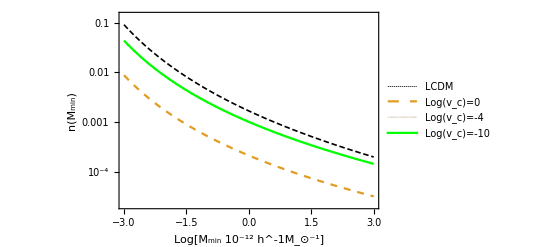

```mathematica
LogPlot[{Evaluate[nM[10^R,1.686,20,10,201]],Evaluate[nM[10^R,1.686,-4,0,201]],Evaluate[nM[10^R,1.686,-4,4,201]],Evaluate[nM[10^R,1.686,-4,10,201]]},{R,-3,3},Frame->True,PlotStyle->{{Black,Dashing[{0.010,0.005}],Thickness[0.003]},Dashed,{Brown,Dashing[{0.001,0.005,0.005,0.005}],Thickness[0.001]},Green,Red},FrameLabel->{"Log[M_min 10^-12 h^-1M_⊙^-1]","n(M_min)",None,None},FrameStyle->Directive[{12}],PlotLegends->{"LCDM","Log(v_c)=0","Log(v_c)=-4","Log(v_c)=-10"}]
```

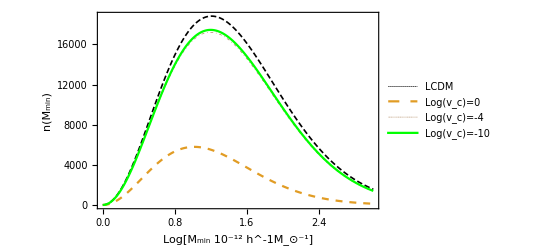

```mathematica
ListPlot[{dNdz[10^0,1.686,20,10,1],dNdz[10^0,1.686,0,0,1],dNdz[10^0,1.686,0,4,1],dNdz[10^0,1.686,0,10,1]},Frame->True,PlotStyle->{{Black,Dashing[{0.010,0.005}],Thickness[0.003]},Dashed,{Brown,Dashing[{0.001,0.005,0.005,0.005}],Thickness[0.001]},Green,Red},FrameLabel->{"Log[M_min 10^-12 h^-1M_⊙^-1]","n(M_min)","a_c=10^-5",None},FrameStyle->Directive[{12}],Joined->True,PlotLegends->{"LCDM","Log(v_c)=0","Log(v_c)=-4","Log(v_c)=-10"}]
```

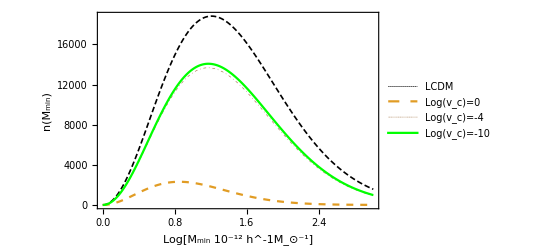

```mathematica
ListPlot[{dNdz[10^0,1.686,20,10,1],dNdz[10^0,1.686,-2,0,1],dNdz[10^0,1.686,-2,4,1],dNdz[10^0,1.686,-2,10,1]},Frame->True,PlotStyle->{{Black,Dashing[{0.010,0.005}],Thickness[0.003]},Dashed,{Brown,Dashing[{0.001,0.005,0.005,0.005}],Thickness[0.001]},Green,Red},FrameLabel->{"Log[M_min 10^-12 h^-1M_⊙^-1]","n(M_min)","a_c=10^-4",None},FrameStyle->Directive[{12}],Joined->True,PlotLegends->{"LCDM","Log(v_c)=0","Log(v_c)=-4","Log(v_c)=-10"}]
```

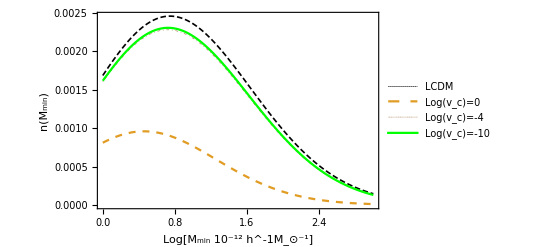

```mathematica
ListPlot[{TablenM[10^0,1.686,20,10,1],TablenM[10^0,1.686,0,0,1],TablenM[10^0,1.686,0,4,1],TablenM[10^0,1.686,0,10,1]},Frame->True,PlotStyle->{{Black,Dashing[{0.010,0.005}],Thickness[0.003]},Dashed,{Brown,Dashing[{0.001,0.005,0.005,0.005}],Thickness[0.001]},Green,Red},FrameLabel->{"Log[M_min 10^-12 h^-1M_⊙^-1]","n(M_min)",None,None},FrameStyle->Directive[{12}],Joined->True,PlotLegends->{"LCDM","Log(v_c)=0","Log(v_c)=-4","Log(v_c)=-10"}]
```

```mathematica
Tabledn[R_,deltac_?NumberQ,l_?NumberQ,j_?NumberQ,znum_?NumberQ]
```

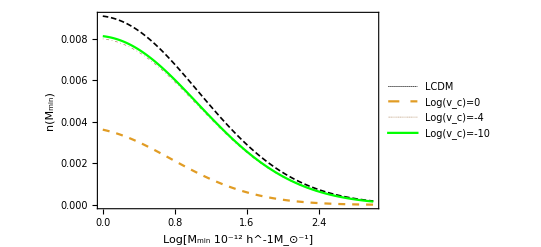

```mathematica
ListPlot[{Tabledn[10^0,1.686,20,10,1],Tabledn[10^0,1.686,0,0,1],Tabledn[10^0,1.686,0,4,1],Tabledn[10^0,1.686,0,10,1]},Frame->True,PlotStyle->{{Black,Dashing[{0.010,0.005}],Thickness[0.003]},Dashed,{Brown,Dashing[{0.001,0.005,0.005,0.005}],Thickness[0.001]},Green,Red},FrameLabel->{"Log[M_min 10^-12 h^-1M_⊙^-1]","n(M_min)",None,None},FrameStyle->Directive[{12}],Joined->True,PlotLegends->{"LCDM","Log(v_c)=0","Log(v_c)=-4","Log(v_c)=-10"}]
```

```mathematica
Needs["NumericalDifferentialEquationAnalysis`"]
```

```mathematica
Export["GaussianQuadratureWeights.dat",GaussianQuadratureWeights[nd,-1,1]];
```

```mathematica
CurrentValue[$FrontEnd,"NotebookAutoSave"]=True
```

True

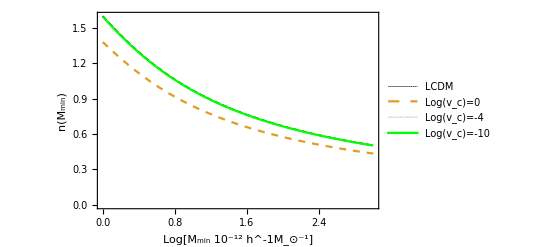

```mathematica
ListPlot[{Tableσ[10^0,20,10,1],Tableσ[10^0,0,0,1],Tableσ[10^0,0,4,1],Tableσ[10^0,0,10,1]},Frame->True,PlotStyle->{{Black,Dashing[{0.010,0.005}],Thickness[0.003]},Dashed,{Brown,Dashing[{0.001,0.005,0.005,0.005}],Thickness[0.001]},Green,Red},FrameLabel->{"Log[M_min 10^-12 h^-1M_⊙^-1]","n(M_min)",None,None},FrameStyle->Directive[{12}],Joined->True,PlotLegends->{"LCDM","Log(v_c)=0","Log(v_c)=-4","Log(v_c)=-10"}]
```

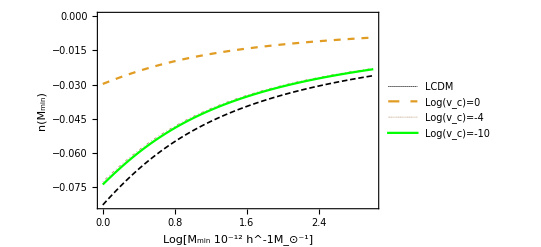

```mathematica
ListPlot[{TableDσ[10^0,20,10,1],TableDσ[10^0,0,0,1],TableDσ[10^0,0,4,1],TableDσ[10^0,0,10,1]},Frame->True,PlotStyle->{{Black,Dashing[{0.010,0.005}],Thickness[0.003]},Dashed,{Brown,Dashing[{0.001,0.005,0.005,0.005}],Thickness[0.001]},Green,Red},FrameLabel->{"Log[M_min 10^-12 h^-1M_⊙^-1]","n(M_min)",None,None},FrameStyle->Directive[{12}],Joined->True,PlotLegends->{"LCDM","Log(v_c)=0","Log(v_c)=-4","Log(v_c)=-10"}]
```

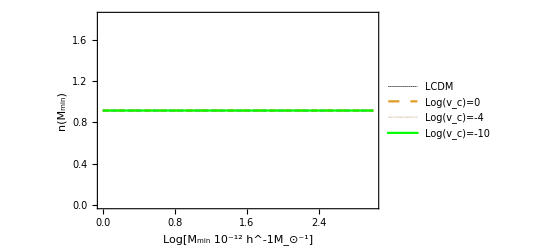

```mathematica
ListPlot[{TableFmasses[10^0,20,10,1],TableFmasses[10^0,0,0,1],TableFmasses[10^0,0,4,1],TableFmasses[10^0,0,10,1]},Frame->True,PlotStyle->{{Black,Dashing[{0.010,0.005}],Thickness[0.003]},Dashed,{Brown,Dashing[{0.001,0.005,0.005,0.005}],Thickness[0.001]},Green,Red},FrameLabel->{"Log[M_min 10^-12 h^-1M_⊙^-1]","n(M_min)",None,None},FrameStyle->Directive[{12}],Joined->True,PlotLegends->{"LCDM","Log(v_c)=0","Log(v_c)=-4","Log(v_c)=-10"}]
```

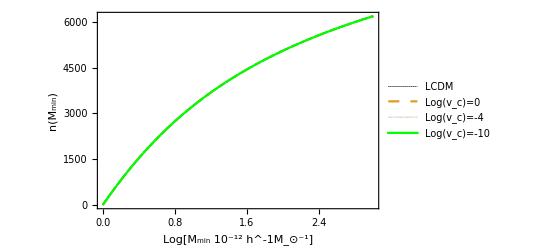

```mathematica
ListPlot[{Tablercom[20,10,1],Tablercom[0,0,1],Tablercom[0,4,1],Tablercom[0,10,1]},Frame->True,PlotStyle->{{Black,Dashing[{0.010,0.005}],Thickness[0.003]},Dashed,{Brown,Dashing[{0.001,0.005,0.005,0.005}],Thickness[0.001]},Green,Red},FrameLabel->{"Log[M_min 10^-12 h^-1M_⊙^-1]","n(M_min)",None,None},FrameStyle->Directive[{12}],Joined->True,PlotLegends->{"LCDM","Log(v_c)=0","Log(v_c)=-4","Log(v_c)=-10"}]
```

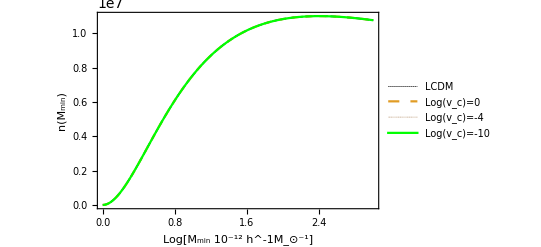

```mathematica
ListPlot[{TabledVdzdΩ[20,10,1],TabledVdzdΩ[0,0,1],TabledVdzdΩ[0,4,1],TabledVdzdΩ[0,10,1]},Frame->True,PlotStyle->{{Black,Dashing[{0.010,0.005}],Thickness[0.003]},Dashed,{Brown,Dashing[{0.001,0.005,0.005,0.005}],Thickness[0.001]},Green,Red},FrameLabel->{"Log[M_min 10^-12 h^-1M_⊙^-1]","n(M_min)",None,None},FrameStyle->Directive[{12}],Joined->True,PlotLegends->{"LCDM","Log(v_c)=0","Log(v_c)=-4","Log(v_c)=-10"}]
```

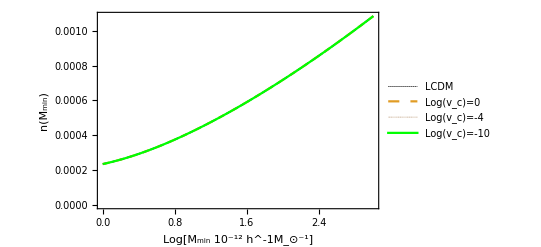

```mathematica
ListPlot[{Tabledhfun[20,10,1],Tabledhfun[0,0,1],Tabledhfun[0,4,1],Tabledhfun[0,10,1]},Frame->True,PlotStyle->{{Black,Dashing[{0.010,0.005}],Thickness[0.003]},Dashed,{Brown,Dashing[{0.001,0.005,0.005,0.005}],Thickness[0.001]},Green,Red},FrameLabel->{"Log[M_min 10^-12 h^-1M_⊙^-1]","n(M_min)",None,None},FrameStyle->Directive[{12}],Joined->True,PlotLegends->{"LCDM","Log(v_c)=0","Log(v_c)=-4","Log(v_c)=-10"}]
```